# AlphaDiskModel

The AlphaDiskModel` package contains function for generating the alpha disk model as described by Shakura and Sunyaev (1972), and Novikov and Thorne in their Les Houches lecture (1973), as well as its observed properties. The public functions in this package are:

DiskParams[a, α, m, mdot, Options] | returns an association containing information about accretion disk's radiation. The keys are 'Temperature', 'SpectralFluxDensity' and 'FluxDensity'.
ObservedDiskElement[disk, geodesic, Options] | returns an association containing information about accretion disk 'disk' (assoc generated by DiskParams) radiation observed on geodesic 'geodesic' (assoc generated by KerrNullGeoDistant). The keys are 'PhysicalTemperature', 'EffectiveTemperature', 'SpecificIntensity', 'Intensity' and 'PeakFrequency'.

First, load the paclet:

```mathematica
Needs["BlackHoleImages`"]
```

## The Conventions in This Package

The disk model used in this Paclet is the one proposed by Shakura and Sunyaev (1972) in their Newtonian treatment with the full relativistic solution taken from Novikov and Thorne's lecture in Les Houches (1973). It is a geometrically thin, optically thick disk allowing us to use the equatorial approximation. The KerrNullGeodesics package is written with this assumption in mind, and for a geometrically thick disk, the structure of the paclet would need to be altered. The assumption of optical thickness requires an effective cooling process in the disk, and thus relatively large matter influx which, nevertheless, should remain under the Eddington limit. Thanks to the radiative cooling, the pressure with its gradient remains low allowing us to approximate the motion of the fluid as equatorial circular time-like geodesics. Circular geodesics lose stability at the innermost stable circular orbit whose radius is R_ISCO, which then also defined the inner edge of the quasi-stationary disk.

The  shear stress in the disk is characterized by the free parameter of the model denoted by α; w_rϕ~ αρv_s^2 , where ρ is the (proper) matter density and v_s the speed of sound in the disk.

The spin parameter of the black hole a is expected to be given in units of the black hole mass throughout the package and only subextremal black holes are treated (a from zero to one).

## The functions

The DiskParams function returns an association containing information about accretion disk's radiation. The following arguments should be specified:

a | The black hole spin parameter.
α | The Shakura-Sunyaev parameter for the efficiency of angular momentum transport in the disk.
m | The mass of the black hole.
mdot | The mass influx (accretion rate).

Additional options can be given:

Option | Default | Description
"InputUnits" | "NovikovThorne" | This option specifies the units in which the user has provided the input. The default option is "InputUnits"->"NovikovThorne", which expects the mass M to be given in geometrized units and the mass influx mdot to be dimensionless, ṁ:=Ṁ/10^14 kg /s. Other accepted options are "InputUnits"->"SI", "InputUnits"->"CGS", and "InputUnits"->"ShakuraSunyaev", the first two expecting SI and CGS units respectively, the last one expecting M to be given in solar masses and mdot to be given in multiples of the critical mass influx; the mass influx at which the Eddington luminosity  is reached.
"OutputUnits" | "SI" |  This option changes the units of the output functions (temperature and flux density). As of April 2025, only the default option "OutputUnits"->"SI" is supported.
"rUnits" | "BHMass" | The output functions of DiskParams are functions of radius. This option changes the units of radius these functions expect. The default option is "rUnits"->"BHMass", which expects the dimensionless r used throughout chapters 1 and 2,  r=Rc^2/(GM), where R is radius with dimension. Other supported options are "rUnits"->"SI", "rUnits"->"CGS", and "rUnits"->"ShakuraSunyaev", the first two using the meters and centimeters as units respectively, and the last one using Shakura and Sunyaev’s definition, r=Rc^2/(6GM).

The function returns an association with the following keys:

"Temperature" | This returns the surface temperature of the disk as a function
of the radius.
 "SpectralFluxDensity" | This returns the spectral flux density of the disk’s radiation as a function of the radiation’s frequency and the radius.
"FluxDensity" | This returns the integrated flux density over the spectrum
as a function of the radius.
"PeakFrequency" | This returns the frequency of the radiation at the peak of
the spectral flux density at a given radius.
"rDefinition" | This returns a factor by which the input must be multiplied if
it is provided in the black hole mass units. This is relevant for communication with other functions of the package and can be largely ignored by the user.
"rISCO" | This returns the radius of the innermost stable circular orbit in the black hole’s mass multiples (geometrized units).

As an example, let us generate the accretion disk near a black hole with the spin parameter a= 0.6, and the solar mass. The disk should be specified by the alpha parameter α=0.1, and the mass influx  10^14 kg /s:

```mathematica
disk = DiskParams[0.6, 0.1, 1500, 1];
```

The disk looses its stability at:

```mathematica
rISCO = disk["rISCO"];
Print["R_ISCO = ", 1500 rISCO, " m"]
```

R_ISCO = 5743.6 m

We can plot the temperature of the disk from R_ISCO to 10^4 R_ISCO on a logarithmic plot:

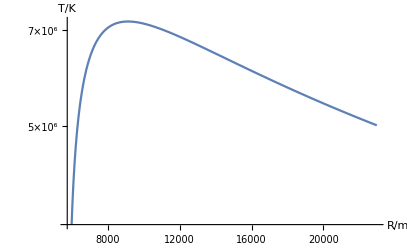

```mathematica
LogPlot[disk["Temperature"][r/1500], {r, 1500 rISCO, 4 1500 rISCO}, AxesLabel->{"R/m", "T/K"}]
```

For generating images of the disk, it is necessary to connect the disk elements with the observer via a null geodesic. For this purpose, the ObservedDiskElement function is implemented. This function is independent of the underlying disk model, provided the disk remains equatorial. The parameters of this function are:

disk | Association generated by the DiskParamsfunction or equivalent.
geodesic | Association generated by the KerrNullGeoDistant function or equivalent.

The following option can be given:

Option | Default | Description
"Grid" | False | Specifies whether a grid of lines of constant r and φ should be generated over the data. Takes a Boolean value.

The function returns an association with the following keys:

"PhysicalTemperature" | This returns the surface temperature at the coordinates passed to the function through the geodesic object in geodesic["EmissionCoordinates"] .
"EffectiveTemperature" | This returns the temperature at which a black body with the observed intensity would raiate according to the Stefan-Boltzmann law.
"SpecificIntensity" | Returns the specific intensity calculated from disk["SpectralFluxDensity"] at the radius given by geodesic["EmissionCoordinates"] as a function of frequency, as it would be measured by the observer.
"Intensity" | Returns the integrated specific intensity given by
disk["FluxDensity"]/π at the radius given by geodesic["EmissionCoordinates"]
as it would be measured by the observer.
"PeakFrequency" | Returns the peak frequency given by given by disk["PeakFrequency"] at the radius given by geodesic["EmissionCoordinates"] as it would be measured by the observer.

As an example, let us use the same disk we generated in the previous example and see, how the radiative properties would appear to a distant observer at the polar coordinate θo = π/4 who looks in the direction of a null geodesic specified by the Bardeen coordinates (10, 10):

```mathematica
geodesic = KerrNullGeoDistant[0.6, π/4, 10, 10];
element = ObservedDiskElement[disk, geodesic, "Grid"->False];
```

We can compare the physical temperature of the disk and the effective temperature:

```mathematica
Tphys = element["PhysicalTemperature"];
Teff = element["EffectiveTemperature"];
Print["T_phys = ", Tphys, " K > ", Teff, " K = T_eff"]
```

T_phys = 5.29533×10^6 K > 4.14285×10^6 K = T_eff

Since the physical temperature is larger, we can guess, that the elements moves away from the observer, although since the radiation is not Planckian all over the disk, this cannot be said for sure without a larger picture.

The measured intensity coming from the disk element is:

```mathematica
Q = element["Intensity"];
Print["Q = ", Q, " J/cm^2/s/ster"]
```

Q = 5.31687×10^18 J/cm^2/s/ster

We can plot the specific intensity as a function of the frequency and verify that the calculated peak frequency maches the plot's peak:

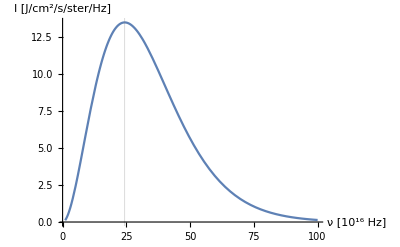

```mathematica
Plot[element["SpecificIntensity"][10^16 ν], {ν, 1, 100}, GridLines->{{element["PeakFrequency"]/10^16},{}}, AxesLabel->{"ν [10^16 Hz]","I [J/cm^2/s/ster/Hz]"}]
```

Related Guides

AlphaDiskModel

Related Tech Notes

KerrImages

KerrNullGeodesics

## Metadata

### Categorization

Tech Note

BlackHoleImages

BlackHoleImages`

BlackHoleImages/tutorial/AlphaDiskModel

### Keywords